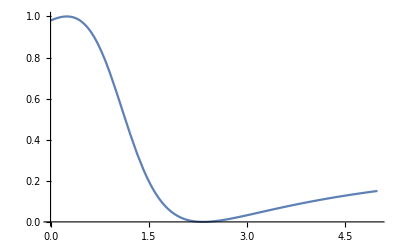

```mathematica
Plot[(r^2 (ω - 1)^2 + t^2 - 2 r t (ω - 1))/((ω - 1)^2+1) //. {t -> √(1-r^2)} //. r -> 0.6, {ω, 0, 5}]
```

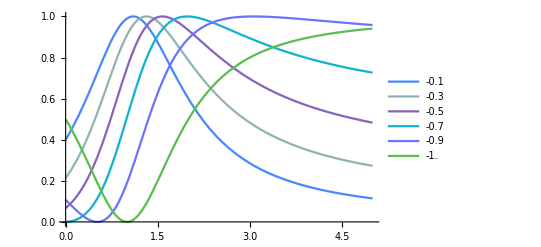

```mathematica
(*The Evaluate function call is needed to make Plot color the curves differently: otherwise Plot just recognize Plot[Map[...]] as a whole and apply one color to all curves.*)
rrange = {-0.1, -0.3, -0.5, -0.7, -0.9, -1.0};
ω0 = 1.0;
Plot[Evaluate[Map[((r^2 (ω - ω0)^2 + t^2 - 2 r t (ω - ω0))/((ω - ω0)^2+1) //. {t -> √(1-r^2)} //. r -> #1)&, rrange]], {ω, 0, 5}, PlotTheme->"CoolColor", PlotLegends-> rrange]
```